# Poisson Distribution

Number of Attempts:

Avg Number of Successes:

Plot!

Print Distribution List

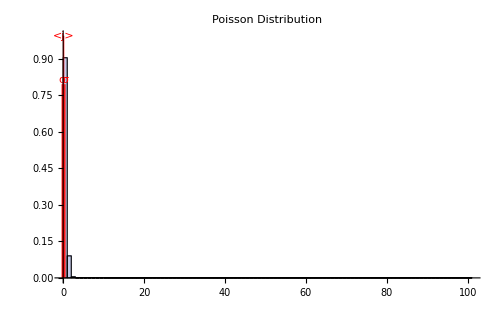

Avg=0.1

σ=0.316228

```mathematica
P=Po=N[(a^0/0!)*ⅇ^-a];
Poisson=Prepend[Freq=Table[P=a/(j)*P,{j,1,n}],Po];
Needs["Histograms`"];
Show[Histogram[Poisson,FrequencyData->True,ImageSize->500],Graphics[{RGBColor[1,0,0],Line[{{a,0},{a,Max[Poisson]+.1Max[Poisson]}}],Text["<j>",{a,Max[Poisson]+.1Max[Poisson]}],Line[{{a+Sqrt[a],0},{a+Sqrt[a],Max[Poisson]-.12Max[Poisson]}}],Text["σ",{a+Sqrt[a],Max[Poisson]-.1Max[Poisson]}],Line[{{a-Sqrt[a],0},{a-Sqrt[a],Max[Poisson]-.12Max[Poisson]}}],Text["σ",{a-Sqrt[a],Max[Poisson]-.1Max[Poisson]}]}],PlotLabel->"Poisson Distribution"]
Print["Avg=",a]
Print["σ=",N[Sqrt[a]]]
```